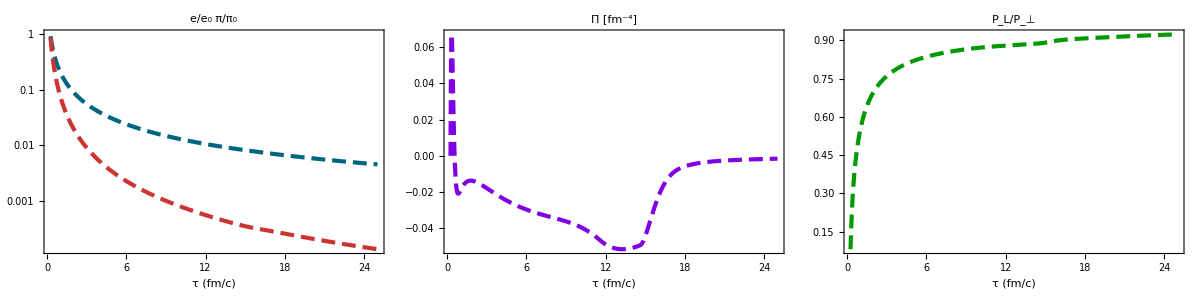

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

styles={Directive[RGBColor[0,0.4,0.5],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0.8,0.2,0.2],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],
Directive[RGBColor[0.5,0.0,0.9],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0.0,0.6,0.0],AbsoluteThickness[3],AbsoluteDashing[{10,5}]]};

EnergyDensityDataRaw=Import[wd<>"/eplot.dat"];
piDataRaw=Import[wd<>"/piplot.dat"];
PiDataRaw=Import[wd<>"/bulkplot.dat"];
plptDataRaw=Import[wd<>"/plptplot.dat"];

EnergyDensityData= Take[EnergyDensityDataRaw,{2,Length[EnergyDensityDataRaw]}];
piData= Take[piDataRaw,{2,Length[piDataRaw]}];
PiData= Take[PiDataRaw,{2,Length[PiDataRaw]}];
plptData= Take[plptDataRaw,{2,Length[plptDataRaw]}];

t0 = EnergyDensityData[[1,1]];
tf = EnergyDensityData[[Length[EnergyDensityData],1]];

energydensity = Interpolation[EnergyDensityData[[All,{1,2}]]];
pi = Interpolation[piData[[All,{1,2}]]];
bulk = Interpolation[PiData[[All,{1,2}]]];
plpt = Interpolation[plptData[[All,{1,2}]]];

Print[Grid[{{LogPlot[{energydensity[t],pi[t]},{t,t0+0.02,tf},PlotRange->{0.0,1},PlotStyle->styles[[1;;2]],ImageSize->400,Frame->True,Axes->False,PlotLabel->Style["e/e_0         π/π_0",FontSize->24],FrameLabel->{"τ (fm/c)",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{bulk[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[3]],ImageSize->400,Frame->True,Axes->False,PlotLabel->Style["Π [fm^-4]",FontSize->24],FrameLabel->{"τ (fm/c)",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{plpt[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[4]],ImageSize->400,Frame->True,Axes->False,PlotLabel->Style["P_L/P_⊥",FontSize->24],FrameLabel->{"τ (fm/c)",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]]
```

```mathematica
z
```